# Thunderstorm Analyzer

ABSTRACT:
The goal of this project is the creation of a system which will automatically get the data from public weather servers, analyze quantities like the number of cosmic rays, levels of ionizing radiation, electrostatic field strength, etc., and study their temporal correlation to detect the cases of Thunderstorm ground enhancements (TGE).
Thunderstorm ground Enhancement is a process of increase in the level of gamma radiation, number of electrons and neutrons, connected to the propagation of cosmic rays through strong atmospheric electric fields.
It was observed that during thunderstorms electrostatic field increases by orders of magnitude and gamma radiation levels as well as number of neutrons and relativistic electrons increase up to 10 times above cosmic ray background. When electrostatic field reaches certain levels lightning happens and the level of gamma radiation, electrons and neutrons as well as the field itself fall down immediately after the lightning.
The TGE events are characterized by following 7 criteria:

Large fluxes of electrons and gamma rays with durations around 10 minutes;

Increase in neutron number;

Microsecond electron bursts with around 50ms duration;

Increase of high energy muon level;

Large, usually negative, near-surface electric field, rising sometimes from deep negative to near zero positive values. Usually field is at the level of -10 - -30 kV/m;

Decrease of the cloud-ground lightnings and increase of intracloud lightnings.

Increase of relative humidity above 80% and decrease of air temperature below 5-6 degrease Celsius.

The system should analyze all the data and look for this kind of events and notify us upon their occurring.

## Import Electric Field Data from csv file.

#### Delete empty strings, corrupted sublists and the first element of the list which contains header of csv file.

```mathematica
electricField=DeleteCases[
DeleteCases[
Delete[
Import["C:\\Users\\Administrator\\Desktop\\Wolfram Summer School Armenia 2016\\Project\\Data\\EField.csv"],1
],
"",{2}],{_,_,__}|{}];
```

```mathematica
splitted=StringSplit[electricField[[All,1]],":"|" "];
```

#### Convert all first three elements of sublists to expressions

```mathematica
expr1=MapAt[ToExpression,splitted,{All,{1,2,3}}];
```

#### Construct the list of Time Series. Convert strings that contain time to the format of {h,m,s} and hour running from 0 to 24.

```mathematica
eFieldTime=Map[
TimeObject[Which[
#[[4]]==="PM"&&#[[1]]=!=12,
{#[[1]]+12,#[[2]],#[[3]]},
#[[1]]===12,
{0,#[[2]],#[[3]]},
True,
Most[#]
]]&,expr1];
```

```mathematica
eFieldTime=Map[
Which[
#[[4]]==="PM"&&#[[1]]=!=12,
{2016,08,1,#[[1]]+12,#[[2]],#[[3]]},
#[[1]]===12,
{2016,08,1,0,#[[2]],#[[3]]},
True,
Join[{2016,08,1},Most[#]]
]&,expr1];
```

#### Construct the list of data points.

```mathematica
eFieldData=DeleteCases[Flatten[electricField,2],_String];
```

#### Construct the Time Series and plot it.

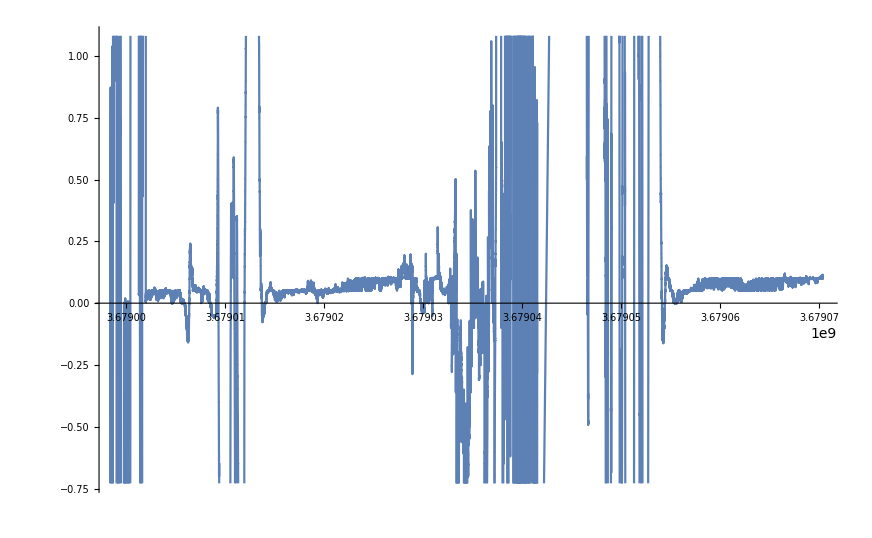

```mathematica
eFieldTimeSeries=TimeSeries[eFieldData,{eFieldTime}];
ListLinePlot[eFieldTimeSeries]
```